Last modified on: Tuesday, July 10, 2018 at 13:26

Author Info

Madeleine Sutherland

Paul Abbott

Massachusetts Institute of Technology
Collaborator: Robert Nachbar

Poster Session Content

Interpreting Drug Quantitative Structure-Activity Relationship (QSAR) Data in Mathematica

Investigate the applicability of WL machine learning and other functionality to the analysis of drug QSAR data. Build models that can be applied to experimental design in the real world.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

-Graphics-

• Wolfram Language streamlines statistical analysis of complicated, multivariate data
• We are able to use calculated atomic coordinates to generate 3D images of molecules
• We can then map continuous variables such as electronegativity over the grid
• Molecular descriptors can be fed into neural nets, but with sparse chemical diversity the net doesn’t come up with an improved model

• Generate more chemically diverse data sets, try feeding them into a neural net
• Map calculated electron density data over 3D chemical structure grid
• Test ability of neural net to predict target engagement of drug structures from rich, structurally diverse SAR data.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Section Header

Type text here

Section Header

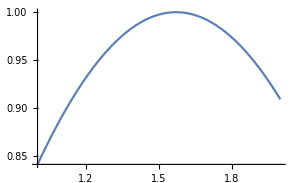
Plot[Sin[x],{x,1,2}]
-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

#### Code

Provide one of:

Link to the GitHub

Explicit code

#### Written Content / Lesson Plans

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

#### Future Directions

#### Background Info Links/References

#### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

#### Other information

## Project Summary

My project will test the ability of a neural net to perform a Quantitative Structure-Activity Relationship (QSAR) study on a series of phenylalkylamine drugs.
In QSAR, data on the structure and properties of structurally related compounds with known biochemical activity are used to build a model to predict the activity of additional compounds in that series. Traditional descriptors have included the octanol/water partition coefficient LogP, molecular weight and Total Polar Surface Area (TPSA) and two-dimensional structure. In the past couple years, there has been increasing interest in use of three-dimensional, energetically optimized structure and quantum chemical descriptors from Density Functional Theory (DFT) calculations. Anecdotally, such descriptors have led to models with good fit.
Here, we are working with phenylalkylamines, whose mechanism of action and binding mode is unknown. So, we will first create z-matrices for the structures of the compound with all the possible combinations of cis and trans conformations of each substituent on the ring with respect to the alkylamine substituent. We will align all the conformations of the compounds with respect to a reference, and see if one conformation gives particularly good agreement across this series of active drugs. If so, that conformation will be used for all the compounds in the series.
Then, we will convert the z-matrices into 3D image matrices via the hard sphere model, and assign voxels corresponding to atomic number at the appropriate atomic radius around each atom. 
A training set of those 3D images and the biochemical activities of their respective compounds will then be fed into Predict[], since biochemical activity is a continuous variable (in this case, logMU, the log of effective doses of the compound in question and mescaline). 
We will analyze the resulting model with respect to its ability to predict the biochemical activities of the remaining test set of compounds. 
We hope to create a generalizeable framework that can be applied to additional data set.  In the future, we could perform a meta-analysis to see what types of variables/descriptors make the most robust QSAR models in the context of machine learning.